```mathematica
r[θ_]:=RotationTransform[θ °]
```

```mathematica
r[60]
```

TransformationFunction[(1/2 | -(√3)/2 | 0
(√3)/2 | 1/2 | 0
0 | 0 | 1)]

```mathematica
Manipulate[Graphics[
{LightGray,Opacity[0.5],r[θ]@Rectangle[{0,0},{10,3}],
Red,Arrow[r[2θ]@{{0,0},{4,4}}]
},
GridLines->Automatic,
Axes->Automatic,
PlotRange->{{-2,10},{-2,10}}],{θ,0,90}]
```



```mathematica
Graphics@Circle[]
```

```mathematica
-Graphics-//InputForm
```

Graphics[Circle[{0, 0}]]

```mathematica
-Graphics-//InputForm
```

```mathematica
s@Rectangle[{0,0},{10,3}]
```

Polygon[…]

```mathematica
Arrow[s@{{0,0},{4,4}}]
```

Arrow[{{0,0},{2-2 √3,2+2 √3}}]

```mathematica
Line[s@{{0,0},{4,4}}]
```

Line[{{0,0},{2-2 √3,2+2 √3}}]

```mathematica
s@Line[{{0,0},{4,4}}]/.Line->Arrow
```

Arrow[{{{0,0},{2-2 √3,2+2 √3}}}]

```mathematica
s@Arrow[{{0,0},{4,4}}]
```

TransformationFunction[(1/2 | -(√3)/2 | 0
(√3)/2 | 1/2 | 0
0 | 0 | 1)][Arrow[{{0,0},{4,4}}]]

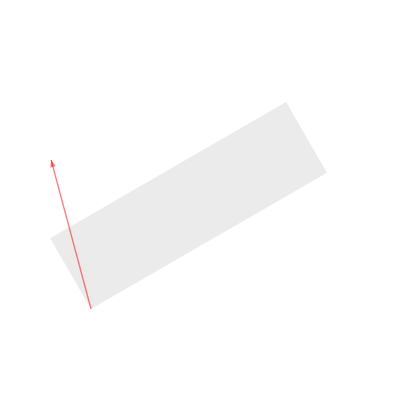

```mathematica
Graphics[
{LightGray,Opacity[0.5],r@Rectangle[{0,0},{10,3}],
Red,s@Line[{{0,0},{4,4}}]/.Line->Arrow
},
GridLines->Automatic,
Axes->Automatic,
PlotRange->{{-2,10},{-2,10}}]
```